## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW170814";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
samples["dalpha_3"][[6]]
```

## m1-m2 Plot, 22

```mathematica
plots=<||>;
compPlots=<||>;
```

## INSPIRAL

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00471};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 14630 + 镜像 14630

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.70852×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.70852×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.00471}，共 2 条

第一条前3点：{{32.1275,32.7915},{32.0223,32.8867},{31.9147,32.9842}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.578477

可信水平百分比：57.8477%

==========================

dphi_2 预处理完成，红线包含概率 prob = 0.578477

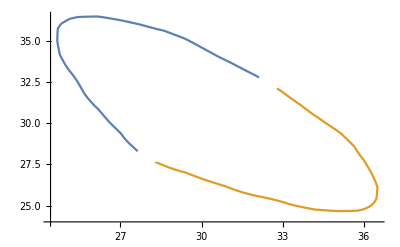

```mathematica
ListLinePlot[contourPoints[p]]
```

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
samples[p][[6]]
```

```mathematica
prob
```

0.578477

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.210761, 0.789239}

实际使用的 GR 概率区间上下界: {6.39562, 6.4401}

实际使用的 Param 概率区间上下界: {4.23717, 6.38803}

GR下界: 点数=400 | Y>0点数=400 | 平均误差=8.41549×10^-16

GR上界: 点数=400 | Y>0点数=400 | 平均误差=8.54872×10^-16

Param下界: 点数=400 | Y>0点数=400 | 平均误差=0.676859

Param上界: 点数=400 | Y>0点数=400 | 平均误差=2.62013×10^-16

{{10.1,9.11884×10^6},{10.2,9.20912×10^6},{10.3,9.29941×10^6},{10.4,9.38972×10^6},{10.5,9.48×10^6}}

{{10.1,14.7644},{10.2,14.9106},{10.3,15.0568},{10.4,15.203},{10.5,15.3492}}

chi1L取值：0.565796

chi2L取值：0.471965

=====================================================

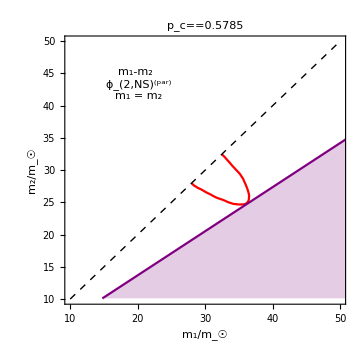

```mathematica
probability=prob;
(*probability=0.5;*)

plots[p]=PlotInversion[p,probability,10,50,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0090825};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 21964 + 镜像 21964

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 2.62006×10^-6 for the integral and error estimates.

对称先验空间积分 = 0.999999（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.62006×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.0090825}，共 2 条

第一条前3点：{{28.9869,29.6497},{28.9826,29.655},{28.9731,29.6695}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.342445

可信水平百分比：34.2445%

==========================

dphi_4 预处理完成，红线包含概率 prob = 0.342445

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.342445

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.328777, 0.671223}

实际使用的 GR 概率区间上下界: {45.9561, 46.196}

实际使用的 Param 概率区间上下界: {5.06133, 46.0154}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=3.72324×10^-15

GR上界: 点数=250 | Y>0点数=250 | 平均误差=3.55271×10^-15

Param下界: 点数=250 | Y>0点数=250 | 平均误差=25.0421

Param上界: 点数=250 | Y>0点数=250 | 平均误差=7.61702×10^-15

{{20.1,4.32295×10^6},{20.2,4.34447×10^6},{20.3,4.36597×10^6},{20.4,4.38748×10^6},{20.5,4.40898×10^6}}

{{20.1,25.1066},{20.2,25.2315},{20.3,25.3564},{20.4,25.4813},{20.5,25.6062}}

chi1L取值：0.55002

chi2L取值：0.510413

=====================================================

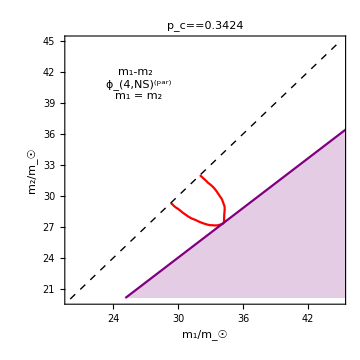

```mathematica
probability=prob;
(*probability=0.33;*)

plots[p]=PlotInversion[p,probability,20,45,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],1]}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_5l"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{15,60},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0107142};
contourPD[p]={0.0107139};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{15,60}

输入q范围：{1,5}

m1范围：{17.2305,163.444}

m2范围：{8.17221,68.9219}

对称数据：原始 20374 + 镜像 20374

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{8.17221, 163.444} × {8.17221, 163.444}

等高线值：{0.0107139}，共 2 条

第一条前3点：{{29.7308,30.216},{29.645,30.3096},{29.5811,30.3627}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.19231

可信水平百分比：19.231%

==========================

dphi_5l 预处理完成，红线包含概率 prob = 0.19231

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.192292

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.40385, 0.59615}

实际使用的 GR 概率区间上下界: {464.851, 464.992}

实际使用的 Param 概率区间上下界: {464.899, 558.482}

GR下界: 点数=650 | Y>0点数=650 | 平均误差=4.28512×10^-14

GR上界: 点数=650 | Y>0点数=650 | 平均误差=5.71932×10^-14

Param下界: 点数=650 | Y>0点数=650 | 平均误差=3.0608×10^-14

Param上界: 点数=650 | Y>0点数=650 | 平均误差=76.7097

{{25.02,30.0591},{25.04,30.0831},{25.06,30.1071},{25.08,30.1312},{25.1,30.1552}}

{{25.02,2.22×10^6},{25.04,2.2218×10^6},{25.06,2.22359×10^6},{25.08,2.22537×10^6},{25.1,2.22714×10^6}}

chi1L取值：0.570095

chi2L取值：0.468785

=====================================================

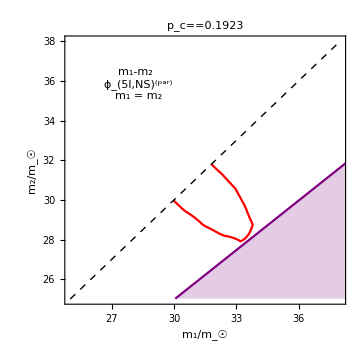

```mathematica
probability=prob;
probability=0.1923;

plots[p]=PlotInversion[p,probability,25,38,0.02,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiLNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{20,50}, {1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.012844};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2.5]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{20,50}

输入q范围：{1,3}

m1范围：{22.974,102.384}

m2范围：{13.6512,57.4349}

对称数据：原始 23399 + 镜像 23399

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.51404×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.51404×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{13.6512, 102.384} × {13.6512, 102.384}

等高线值：{0.012844}，共 2 条

第一条前3点：{{30.8223,30.545},{30.8415,30.518},{30.8721,30.4746}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.117584

可信水平百分比：11.7584%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.117584

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.117584

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.441208, 0.558792}

实际使用的 GR 概率区间上下界: {-1099.63, -1096.3}

实际使用的 Param 概率区间上下界: {-1099.4, -870.071}

GR下界: 点数=650 | Y>0点数=650 | 平均误差=1.48667×10^-13

GR上界: 点数=650 | Y>0点数=650 | 平均误差=1.71755×10^-13

Param下界: 点数=650 | Y>0点数=650 | 平均误差=1.21033×10^-13

Param上界: 点数=650 | Y>0点数=650 | 平均误差=1.45694×10^-13

{{25.02,29.1145},{25.04,29.1378},{25.06,29.1611},{25.08,29.1843},{25.1,29.2076}}

{{25.02,81.9894},{25.04,82.055},{25.06,82.1205},{25.08,82.1861},{25.1,82.2516}}

chi1L取值：0.477754

chi2L取值：0.533642

=====================================================

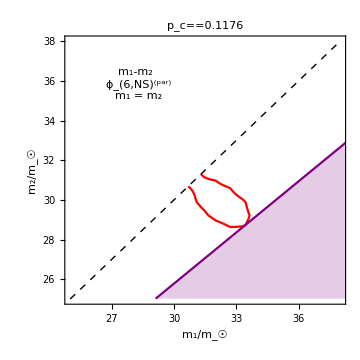

```mathematica
probability=prob;
(*probability=0.1;*)

plots[p]=PlotInversion[p,probability,25,38,0.02,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_7"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{20,50}, {1, 3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.01434};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{20,50}

输入q范围：{1,3}

m1范围：{22.974,102.384}

m2范围：{13.6512,57.4349}

对称数据：原始 22418 + 镜像 22418

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{13.6512, 102.384} × {13.6512, 102.384}

等高线值：{0.01434}，共 2 条

第一条前3点：{{30.7211,30.4443},{30.7218,30.4445},{30.7694,30.4243}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.0569196

可信水平百分比：5.69196%

==========================

dphi_7 预处理完成，红线包含概率 prob = 0.0569196

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.0569196

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.4716, 0.5284}

实际使用的 GR 概率区间上下界: {1129.59, 1129.91}

实际使用的 Param 概率区间上下界: {1130.55, 1491.37}

GR下界: 点数=650 | Y>0点数=650 | 平均误差=7.34592×10^-15

GR上界: 点数=650 | Y>0点数=650 | 平均误差=1.11588×10^-13

Param下界: 点数=650 | Y>0点数=650 | 平均误差=2.62354×10^-14

Param上界: 点数=650 | Y>0点数=650 | 平均误差=360.478

{{25.02,27.482},{25.04,27.504},{25.06,27.526},{25.08,27.548},{25.1,27.5699}}

{{25.02,25.0202},{25.04,25.0401},{25.06,25.0599},{25.08,25.0798},{25.1,25.0997}}

chi1L取值：0.530752

chi2L取值：0.437991

=====================================================

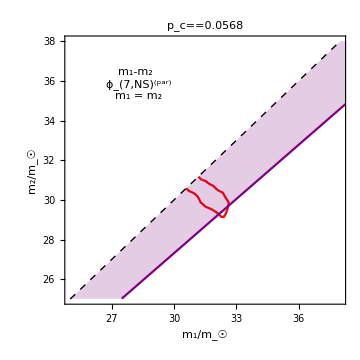

```mathematica
p="dphi_7"; 
probability=prob;
probability=0.0568;
(*0.32*)
plots[p]=PlotInversion[p,probability,25,38,0.02,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},upStyle->Directive[Purple,Opacity[0]]]
```

```mathematica
samples["dphi_7"][[7]]
```

## Intermediate

### beta_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{20,60}, {1, 3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.01175};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{20,60}

输入q范围：{1,3}

m1范围：{22.974,122.86}

m2范围：{13.6512,68.9219}

对称数据：原始 20530 + 镜像 20530

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.999997（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{13.6512, 122.86} × {13.6512, 122.86}

等高线值：{0.01175}，共 2 条

第一条前3点：{{30.2801,30.6214},{30.2244,30.6869},{30.1843,30.734}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.251454

可信水平百分比：25.1454%

==========================

dbeta_2 预处理完成，红线包含概率 prob = 0.251454

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.251454

====== [dbeta_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.374273, 0.625727}

实际使用的 GR 概率区间上下界: {-3.45133, -3.13737}

实际使用的 Param 概率区间上下界: {-3.2965, -2.90666}

GR下界: 点数=650 | Y>0点数=650 | 平均误差=0.151441

GR上界: 点数=650 | Y>0点数=650 | 平均误差=8.98427×10^-16

Param下界: 点数=650 | Y>0点数=650 | 平均误差=1.10476×10^-15

Param上界: 点数=650 | Y>0点数=650 | 平均误差=8.3967×10^-16

{{25.02,30.1144},{25.04,30.1384},{25.06,30.1625},{25.08,30.1866},{25.1,30.2107}}

{{25.02,64.5063},{25.04,64.5579},{25.06,64.6094},{25.08,64.661},{25.1,64.7126}}

chi1L取值：0.599098

chi2L取值：0.414058

=====================================================

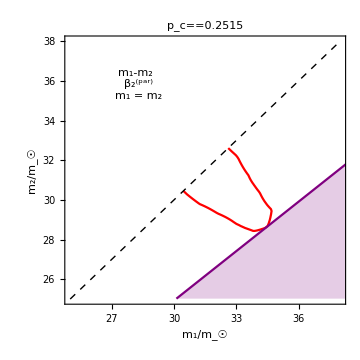

```mathematica
probability=prob;
(*probability=0.101;*)

plots[p]=PlotInversion[p,probability,25,38,0.02,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### beta_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{20,60}, {1, 3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.01467};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],1.5]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{20,60}

输入q范围：{1,3}

m1范围：{22.974,122.86}

m2范围：{13.6512,68.9219}

对称数据：原始 19413 + 镜像 19413

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{13.6512, 122.86} × {13.6512, 122.86}

等高线值：{0.01467}，共 2 条

第一条前3点：{{30.4305,30.0895},{30.4307,30.0895},{30.5039,30.0372}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.185304

可信水平百分比：18.5304%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.185304

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.185304

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.407348, 0.592652}

实际使用的 GR 概率区间上下界: {-0.0000150481, -0.0000142117}

实际使用的 Param 概率区间上下界: {-0.0000165095, -0.0000148161}

GR下界: 点数=650 | Y>0点数=650 | 平均误差=1.46472×10^-21

Greater::nord: Invalid comparison with 25.02-2.18707×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with 25.04-4.64695×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with 25.06+4.66918×10^-14 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR上界: 点数=650 | Y>0点数=0 | 平均误差=5.13828×10^-7

Param下界: 点数=650 | Y>0点数=650 | 平均误差=1.72534×10^-21

Param上界: 点数=650 | Y>0点数=650 | 平均误差=1.76704×10^-21

{{25.02,292.374},{25.04,292.608},{25.06,292.842},{25.08,293.075},{25.1,293.309}}

{{25.02,29.7362},{25.04,29.76},{25.06,29.7837},{25.08,29.8075},{25.1,29.8313}}

chi1L取值：0.621387

chi2L取值：0.446703

=====================================================

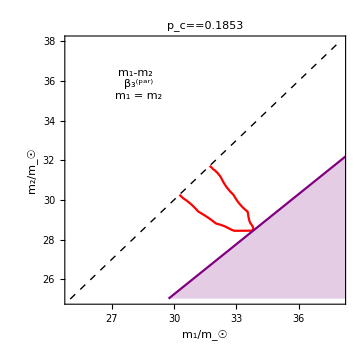

```mathematica
probability=prob;
(*probability=0.17;*)

(* 蓝色要对称一下 *)
plots[p]=PlotInversion[p,probability,25,38,0.02,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

# Merger-RingDown

### alpha_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.000505};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,3}

m1范围：{11.487,163.814}

m2范围：{6.82558,91.8959}

对称数据：原始 17253 + 镜像 17253

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.5111×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.5111×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{6.82558, 163.814} × {6.82558, 163.814}

等高线值：{0.000505}，共 2 条

第一条前3点：{{29.3169,28.8263},{29.3695,28.7968},{29.4753,28.7335}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.947099

可信水平百分比：94.7099%

==========================

dalpha_2 预处理完成，红线包含概率 prob = 0.947099

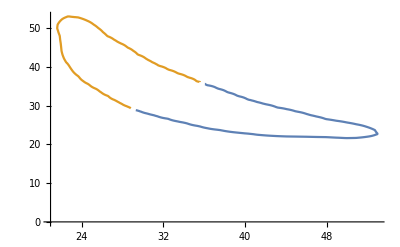

```mathematica
ListLinePlot[contourPoints[p]]
```

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0264505, 0.97355}

实际使用的 GR 概率区间上下界: {-0.0917542, -0.0605843}

实际使用的 Param 概率区间上下界: {-0.0745679, 0.0281705}

GR下界: 点数=550 | Y>0点数=550 | 平均误差=0.0136816

GR上界: 点数=550 | Y>0点数=550 | 平均误差=7.77156×10^-18

Param下界: 点数=550 | Y>0点数=550 | 平均误差=1.40544×10^-17

Param上界: 点数=550 | Y>0点数=550 | 平均误差=0.0561252

{{10.1,24.0869},{10.2,24.3253},{10.3,24.5638},{10.4,24.8023},{10.5,25.0408}}

{{10.1,5.58911×10^6},{10.2,5.64447×10^6},{10.3,5.69979×10^6},{10.4,5.75516×10^6},{10.5,5.81048×10^6}}

chi1L取值：0.68359

chi2L取值：0.56241

=====================================================

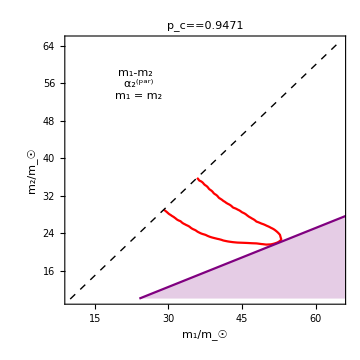

```mathematica
probability=prob;
(*probability=0.95;*)

plots[p]=PlotInversion[p,probability,10,65,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### alpha_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.001235};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.85738

可信水平百分比：85.738%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.85738

输入Mc范围：{10,80}

输入q范围：{1,3}

m1范围：{11.487,163.814}

m2范围：{6.82558,91.8959}

对称数据：原始 19265 + 镜像 19265

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.07764×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.07764×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{6.82558, 163.814} × {6.82558, 163.814}

等高线值：{0.001235}，共 2 条

第一条前3点：{{29.0235,29.5131},{29.0208,29.5114},{28.9632,29.5593}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.85738

可信水平百分比：85.738%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.85738

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.85738

====== [dalpha_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0713101, 0.92869}

实际使用的 GR 概率区间上下界: {-47.6383, -18.9337}

实际使用的 Param 概率区间上下界: {-25.9524, 86.456}

GR下界: 点数=500 | Y>0点数=500 | 平均误差=14.1899

GR上界: 点数=500 | Y>0点数=500 | 平均误差=1.78773×10^-14

Param下界: 点数=500 | Y>0点数=500 | 平均误差=1.71099×10^-14

Param上界: 点数=500 | Y>0点数=500 | 平均误差=79.6423

{{10.1,21.5372},{10.2,21.7505},{10.3,21.9637},{10.4,22.1769},{10.5,22.3902}}

{{10.1,714623.},{10.2,721700.},{10.3,728773.},{10.4,735850.},{10.5,742926.}}

chi1L取值：0.66366

chi2L取值：0.4686

=====================================================

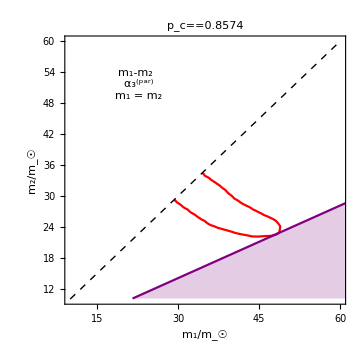

```mathematica
probability=prob;
(*probability=0.87;*)

plots[p]=PlotInversion[p,probability,10,60,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### alpha_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,60}, {1, 3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00285};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,60}

输入q范围：{1,3}

m1范围：{11.487,122.86}

m2范围：{6.82558,68.9219}

对称数据：原始 17070 + 镜像 17070

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.28497×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.28497×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{6.82558, 122.86} × {6.82558, 122.86}

等高线值：{0.00285}，共 2 条

第一条前3点：{{33.565,33.2024},{33.6424,33.1119},{33.6671,33.083}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.643967

可信水平百分比：64.3967%

==========================

dalpha_4 预处理完成，红线包含概率 prob = 0.643967

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.178017, 0.821983}

实际使用的 GR 概率区间上下界: {0.249381, 0.272636}

实际使用的 Param 概率区间上下界: {-0.079826, 0.248744}

GR下界: 点数=400 | Y>0点数=400 | 平均误差=5.66214×10^-17

Greater::nord: Invalid comparison with 15.0548+2.0959 ⅈ attempted.

Greater::nord: Invalid comparison with 15.1539+2.10969 ⅈ attempted.

Greater::nord: Invalid comparison with 15.2529+2.12348 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR上界: 点数=400 | Y>0点数=1 | 平均误差=4.9037×10^-6

Param下界: 点数=400 | Y>0点数=400 | 平均误差=0.0746986

Param上界: 点数=400 | Y>0点数=400 | 平均误差=5.37764×10^-17

{{15.1,2.26314×10^7},{15.2,2.27813×10^7},{15.3,2.29312×10^7},{15.4,2.30811×10^7},{15.5,2.32309×10^7}}

{{15.1,27.2081},{15.2,27.3883},{15.3,27.5685},{15.4,27.7487},{15.5,27.9289}}

chi1L取值：0.505024

chi2L取值：0.506357

=====================================================

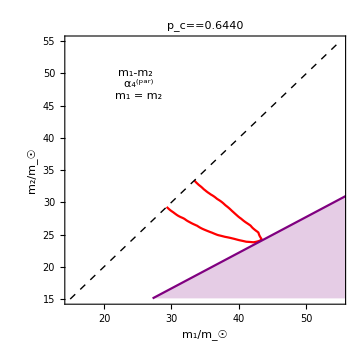

```mathematica
probability=prob;
(*probability=0.4;*)

plots[p]=PlotInversion[p,probability,15,55,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

# utils

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],plots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[plots]}]
```

```mathematica
Directory[]
```

正在导出矢量图: plot_dphi_2.pdf ...

正在导出矢量图: plot_dphi_4.pdf ...

正在导出矢量图: plot_dphi_5l.pdf ...

正在导出矢量图: plot_dphi_6.pdf ...

正在导出矢量图: plot_dphi_7.pdf ...

正在导出矢量图: plot_dbeta_2.pdf ...

正在导出矢量图: plot_dbeta_3.pdf ...

正在导出矢量图: plot_dalpha_2.pdf ...

正在导出矢量图: plot_dalpha_3.pdf ...

正在导出矢量图: plot_dalpha_4.pdf ...